```mathematica
<< NC`
<< NCAlgebra`
<<NCGBX`
com[a_, b_] := a ** b - b ** a;
GBstring[x_] := "'"<> ToString[x]<>"'";
hf[x_] := HoldForm[x ** x - x];
LCChromaticNum[G_, c_] := Module[
{adj, Vnum, rels, gb, GBNPForm, Xindices, GBList},
adj = AdjacencyMatrix[G];
Vnum = Dimensions[adj][[1]];
Xindices = Table[Table[(v-1) * c + i, {i, 1, c}], {v, 1, Vnum}];
Print[Xindices];
GBNPForm = {};
X = Table[Table[ToExpression["X"<>ToString[v]<>ToString[i]], {i, 1, c}], {v, 1, Vnum}];
Print[X];
SetNonCommutative[Flatten[X]];
rels = {};
Do[
GBList = {Table[{Xindices[[v, i]]}, {i, 1, c}], Table[1, {i, 1, c}] };
AppendTo[GBList[[1]], {}];
AppendTo[GBList[[2]], -1];
AppendTo[rels, Sum[X[[v, i]], {i, 1, c}] - 1];
AppendTo[GBNPForm, GBList]
, {v, 1, Vnum}
];
Do[
Do[
GBList = {{{Xindices[[u, i]], Xindices[[u, i]]}, {Xindices[[u, i]]}}, {1, -1}  };
(*AppendTo[
rels, hf[X[[u, i]]]
];*)
AppendTo[
rels, X[[u, i]] ** X[[u, i]] - X[[u, i]]
];
AppendTo[
GBNPForm, GBList
]
, {i, 1, c}
], {u, 1, Vnum}
];
Do[
Do[
Do[
If[
i != j,
GBList = {{{Xindices[[v, i]], Xindices[[v, j]]}}, {1}  };
AppendTo[
rels, X[[v, i]] ** X[[v, j]]
];
AppendTo[
GBNPForm, GBList
]
], {j, 1, c}
], {i, 1, c}
], {v, 1, Vnum}
];
Do[
Do[
Do[
If[
adj[[u, v]] == 1,
GBList = {{{Xindices[[u, i]], Xindices[[v, i]]}}, {1}  };
AppendTo[
rels, X[[u, i]] ** X[[v, i]]
];
AppendTo[
GBNPForm, GBList
]
], {u, 1, Vnum}
], {v, 1, Vnum}
], {i, 1, c}
];
Do[
Do[
Do[
Do[
If[
adj[[u, v]] == 1,
GBList = {{{Xindices[[u, i]], Xindices[[v, j]]}, {Xindices[[v, j]], Xindices[[u, i]]}}, {1, -1}  };
AppendTo[
rels, com[X[[u, i]], X[[v, j]]]
];
AppendTo[
GBNPForm, GBList
]
], {v, 1, Vnum}
], {u, 1, Vnum}
], {j, 1, c}
], {i, 1, c}
];
(*SetMonomialOrder[Flatten[X]];
gb = NCMakeGB[rels, 10];
gb *)
rels 
(*Print[Flatten[X]];
Export["rels.txt", StringReplace[
ToString[
GBNPForm
], {"{" -> "[", "}" -> "]"}
]]*)
(*GBstring @@@ Flatten[X] *)
]
(*g1 = g;*)
(*g= RandomGraph[BernoulliGraphDistribution[6, 0.72], DirectedEdges-> False];
While[
!ConnectedGraphQ[g],
g= RandomGraph[BernoulliGraphDistribution[6, 0.72], DirectedEdges-> False];
]*)
(*g = Graph[{1,2,3,4,5,6},{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6,4<->6,5<->6}]；*)
(*NCPsatz[{0}, result, 1, 1, {}, Flatten[X]]
*)
```

NC::Directory: You are using a paclet version of NCAlgebra.

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

NCPoly::shdw: Symbol NCPoly appears in multiple contexts {NCPoly`,Global`}; definitions in context NCPoly` may shadow or be shadowed by other definitions.

NCPolyDegree::shdw: Symbol NCPolyDegree appears in multiple contexts {NCPoly`,Global`}; definitions in context NCPoly` may shadow or be shadowed by other definitions.

SetMonomialOrder::shdw: Symbol SetMonomialOrder appears in multiple contexts {NCGBX`,Global`}; definitions in context NCGBX` may shadow or be shadowed by other definitions.

NCMakeGB::shdw: Symbol NCMakeGB appears in multiple contexts {NCGBX`,Global`}; definitions in context NCGBX` may shadow or be shadowed by other definitions.

```mathematica
LCCliqueNumber[G_, k_] := Module[
{adj, Vnum, rels, kk, gb = {}},
kk = Round[k];
adj = AdjacencyMatrix[G];
Vnum = Dimensions[adj][[1]];
X = Table[Table[ToExpression["X"<>ToString[i]<>ToString[v]], {v, 1, Vnum}], {i, 1, kk}];
SetNonCommutative[Flatten[X]];
rels = {};
Do[
AppendTo[
rels, Sum[X[[i, v]], {v, 1, Vnum}] - 1
], {i, 1, kk}
];
Do[
Do[
AppendTo[
rels, X[[i, v]] ** X[[i, v]] - X[[i, v]]
]
(*AppendTo[
rels, hf[X[[i, v]]]
]*)
, {v, 1, Vnum}
], {i, 1, kk}
];
Do[
Do[
Do[
If[
u != v,
AppendTo[rels,
X[[i, u]] ** X[[i, v]]
]
], {v, 1, Vnum}
], {u, 1, Vnum}
], {i, 1, kk}
];
Do[
Do[
Do[
Do[
If[
i != j && adj[[u, v]] != 1,
AppendTo[
rels, X[[i, u]] ** X[[j, v]]
]
], {v, 1, Vnum}
], {u, 1, Vnum}
], {j, 1, kk}
], {i, 1, kk}
];
Do[
Do[
Do[
Do[
If[
i != j,
AppendTo[
rels, com[X[[i, u]], X[[j, v]]]
]
], {v, 1, Vnum}
], {u, 1, Vnum}
], {j, 1, kk}
], {i, 1, kk}
];

(*Do[
AppendTo[
rels, Sum[X[[i, v]], {i, 1, kk}]
], {v, 1, Vnum}
];*)

SetMonomialOrder[Flatten[X]];
gb = NCMakeGB[rels, 10];
{gb, rels}
(*rels 
(*gb*)*)

]

Lovasz[G_] := Module[
{adj, stradj, LovaszNumber},
adj = AdjacencyMatrix[G];
stradj = StringReplace[
ToString[Normal[adj]], {"{" -> "[", "}" -> "]"}
];
Export["Lovasz_theta.txt", stradj];
RunProcess[{"python","C:\\Users\\He Entong\\Documents\\LovaszNumber.py"}];
LovaszNumber = Import["C:\\Users\\He Entong\\Documents\\Lovasz_result.txt", "Text"];
(*Print["lovasz number:", LovaszNumber];*)
LovaszNumber
]
```

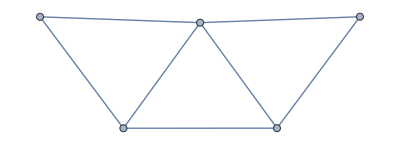

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order:

> X11<X12<X13<X14<X15<X21<X22<X23<X24<X25<X31<X32<X33<X34<X35<X41<X42<X43<X44<X45

* Reduce and normalize initial set

$Aborted

```mathematica
GB = {1->0};
cnt = 0;
While[
GB == {1->0},
density = RandomReal[{0.35, 0.75}];
G= RandomGraph[BernoulliGraphDistribution[5, density], DirectedEdges-> False];
While[
!ConnectedGraphQ[G],
density = RandomReal[{0.35, 0.75}];
G= RandomGraph[BernoulliGraphDistribution[5, density], DirectedEdges-> False];
];
Print[G];
lovasz = Lovasz[GraphComplement[G]];
lovasz = ToExpression[lovasz];
GB = LCCliqueNumber[G, lovasz + 1];
cnt = cnt + 1
]
```

```mathematica
G
```

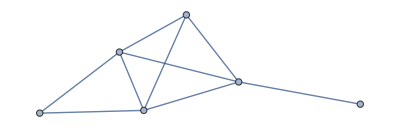
```mathematica
G = -Graphics-；
Gbar= GraphComplement[G];
AdjacencyMatrix[Gbar] // MatrixForm
```

```mathematica
LCCliqueNumber[G, 5]
```

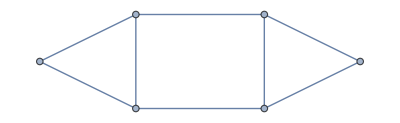
```mathematica
(*G1 = -Graphics-;
LCCliqueNumber[G1, 4]*)

G
```

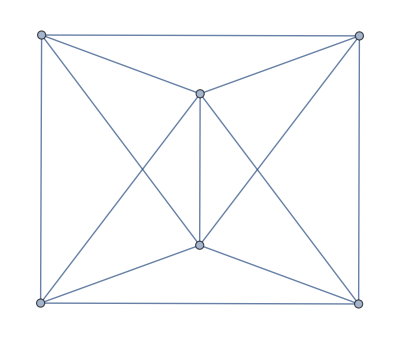
```mathematica
GraphComplement[-Graphics-];
LCCliqueNumber[-Graphics-, 5]
```

```mathematica
c2 = CompleteGraph[2];
Lovasz[GraphComplement[c2]]
GraphComplement[c2]
relsc2 = LCCliqueNumber[c2, 3];
relsc2
(*NCPsatz[{0}, relsc2, 1, 2, {}, Flatten[X]]*)
X
```

```mathematica
c1 = CompleteGraph[1];
Lovasz[GraphComplement[c1]]
GraphComplement[c1]
relsc1 = LCCliqueNumber[c1, 2];
NCPsatz[{0}, relsc1, 1, 1, {}, Flatten[X]]
```

```mathematica
refutationq1 = 
ToExpression[StringReplace[
"[[[0], [0], [-1]], [[-1], [0], [0]], [[0]], [[0]], [[0]], [[1]], [[0]], [[0]]]", {"[" -> "{", "]" -> "}"}
]];
expr1 = 0;
Do[
degh = NCPolyDegree[relsc1[[i]], Flatten[X]];
addexpr1 = (Transpose[refutationq1[[i]]].NCMonoidVec[Flatten[X], 2-degh, {}])[[1, 1]] ** (relsc1[[i]]);
Print[addexpr1, " ", relsc1[[i]]];
expr1 = expr1 + addexpr1
, {i, 1, Length[relsc1]}
 ]
expr1
```

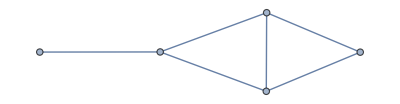

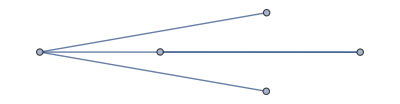

3.0000000030006095

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order:

> X11<X12<X13<X14<X15<X21<X22<X23<X24<X25<X31<X32<X33<X34<X35

* Reduce and normalize initial set

> Initial set reduced to '138' out of '306' polynomials

* Computing initial set of obstructions

> MAJOR Iteration 1, 53 polys in the basis, 60 obstructions

* Found Groebner basis with 53 polynomials

* * * * * * * * * * * * * * * *

{X14→1-X11-X12-X13,X15→0,X24→1-X21-X22-X23,X25→0,X31→1-X11-X21,X33→1-X12-X13-X22-X23-X32,X34→-1+X11+X12+X13+X21+X22+X23,X35→0,X11^2→X11,X11**X12→0,X11**X13→0,X11**X21→0,X12**X11→0,X12^2→X12,X12**X13→0,X12**X22→0,X12**X23→0,X12**X32→0,X13**X11→0,X13**X12→0,X13^2→X13,X13**X21→-1+X11+X12+X13+X21+X22+X23-X11**X22-X11**X23-X12**X21,X13**X22→0,X13**X23→0,X13**X32→0,X21**X11→0,X21**X12→X12**X21,X21**X13→-1+X11+X12+X13+X21+X22+X23-X11**X22-X11**X23-X12**X21,X21^2→X21,X21**X22→0,X21**X23→0,X21**X32→X32-X11**X32,X22**X11→X11**X22,X22**X12→0,X22**X13→0,X22**X21→0,X22^2→X22,X22**X23→0,X22**X32→0,X23**X11→X11**X23,X23**X12→0,X23**X13→0,X23**X21→0,X23**X22→0,X23^2→X23,X23**X32→0,X32**X11→X11**X32,X32**X12→0,X32**X13→0,X32**X21→X32-X11**X32,X32**X22→0,X32**X23→0,X32^2→X32}

```mathematica
GraphComplement[G]
Lovasz[GraphComplement[G]]
rels = LCCliqueNumber[G, 3]
(*Lovasz[GraphComplement[G]]
GraphComplement[G]
rels = LCCliqueNumber[G, 2];*)
```

```mathematica
rules = {X13->1-X11-X12,X11^2->X11,X11**X12->0,X12**X11->0,X12^2->X12}
vv = NCMonoidVec[Flatten[X],2, rels];
```

```mathematica
(*StandardNormalForm[] := Module[ 

 ]*)
```

```mathematica
NCExpandReplaceRepeated[Flatten[NCMonoidVec[Flatten[X], 1, {}]], rels] // MatrixForm
```

(1
X11
X12
1-X11-X12
X21
X22
1-X21-X22
1-X11-X21
1-X12-X22
-1+X11+X12+X21+X22)

```mathematica
B = {{{0, 1, 1, 0}}, {{1, 1, 1, 1}}, {{1, 0, 0, 1}}};
B = Table[Transpose[B[[i]]], {i, 1, Length[B]}];
BB = ConstantArray[0, {3, 3}];
Do[
Do[
BB[[i, j]] = (Transpose[B[[i]]].B[[j]])[[1, 1]], {j, 1, 3}
], {i, 1, 3}
]
BB // MatrixForm
```

(2 | 2 | 0
2 | 4 | 2
0 | 2 | 2)

```mathematica
index[i_, v_, Vnum_] := (i-1)Vnum + v;
ConstructSDP[X_, rels_, adj_] := Module[
{fX, subrels,maxdeg, monoidvec, allterms, basis, d1vec, expr, constexpr, leadtermcoef, coefvec, remaincoefs, returnmat, isomorphism, isovec, coefs, orthorbasis, Vs, vertexvec, Vnum, k, SDPsol, allones},
subrels = rels /. Rule -> Subtract;
fX = Flatten[X];
Vnum = Length[X[[1]]];
k = Length[X];
maxdeg = Max[Table[NCPolyDegree[subrels[[i]], fX], {i, 1, Length[subrels]}]];
monoidvec = NCMonoidVec[fX, maxdeg, rels];
allterms = Flatten[monoidvec];
allterms = Flatten[Table[MonomialList[allterms[[i]]], {i, 1, Length[allterms]}]];
Do[
allterms[[i]] = allterms[[i]] /. (c_.*vars_):>vars, {i, 1, Length[allterms]}
];
basis = {};
Do[
If[
allterms[[i]] == 1,
If[
!MemberQ[basis, 1],
AppendTo[basis, allterms[[i]]]
], ,
If[
!MemberQ[basis, allterms[[i]]],
AppendTo[basis, allterms[[i]]]
]
], {i, 1, Length[allterms]}
];
d1vec = Table[{NCExpandReplaceRepeated[fX[[i]], rels]}, {i, 1, Length[fX]}];
leadtermcoef = Table[0, {i, 1, Length[basis]}];
leadtermcoef[[1]] = 1;
returnmat = {};
Do[
expr = d1vec[[i, 1]];
constexpr = expr /. (Alternatives @@ fX) -> 0;
coefvec = {constexpr};
remaincoefs = Coefficient[NCExpandReplaceRepeated[expr, rels], Table[basis[[j]], {j, 2, Length[basis]}]];
coefvec = Join[coefvec, remaincoefs];
AppendTo[
returnmat, coefvec
], {i, 1, Length[d1vec]}
];

isomorphism = {};
Do[
coefs = returnmat[[i]];
isovec = ConstantArray[{0}, Length[basis]];
Do[
If[
j == 1,
allones = ConstantArray[{1}, Length[basis]];
isovec = isovec + coefs[[j]] * allones,
orthorbasis = ConstantArray[{0}, Length[basis]];
orthorbasis[[j]] = 1;
isovec = isovec + coefs[[j]] * orthorbasis
], {j, 1, Length[coefs]}
];
AppendTo[isomorphism, isovec]
, {i, 1, Length[returnmat]}
];
(*Do[
Print[MatrixForm[isomorphism[[i]]], " ", fX[[i]]], {i, 1, Length[isomorphism]}
];*)
Vs = {};
Print[basis];
Do[
vertexvec = ConstantArray[{0}, Length[basis]];
Do[
vertexvec = vertexvec + isomorphism[[index[i, v, Vnum]]], {i, 1, k}
];
AppendTo[Vs, vertexvec], {v, 1, Vnum}
];
SDPsol = ConstantArray[0, {Vnum, Vnum}];
(*Do[
Print[MatrixForm[Vs[[u]]]], {u, 1, Vnum}
];*)
Do[
Do[
SDPsol[[u, v]] = (Transpose[Vs[[u]]].Vs[[v]])[[1, 1]];
If[
adj[[u, v]] != 1 && SDPsol[[u, v]] != 0 && u < v,
Print["Violation!", {u, v}, MatrixForm[Vs[[u]]], MatrixForm[Vs[[v]]]]
]
, {v, 1, Vnum}
], {u, 1, Vnum}
];
{SDPsol, basis, isomorphism}
]


(*sdp = ConstructSDP[X, rels];*)
```

```mathematica
X
```

{{X11,X12,X13,X14,X15},{X21,X22,X23,X24,X25},{X31,X32,X33,X34,X35}}

```mathematica
GraphComplement[G]
```

-Graphics-

```mathematica
-Graphics-
NCMonoidVec[Flatten[X], 2, rels] // MatrixForm
NCMonoidVec[Flatten[X], 2, rels] // MatrixForm
```

```mathematica
BB = sdp / Tr[sdp];
Tr[BB.ConstantArray[1, {5, 5}]]
```

3

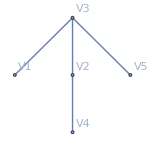
```mathematica
(*vs = 7;
density = RandomReal[{0.35, 0.75}];
rg= RandomGraph[BernoulliGraphDistribution[vs, density], DirectedEdges-> False, VertexLabels->Table[i-> ToExpression["V"<>ToString[i]],{i, vs}]];
While[
!ConnectedGraphQ[rg],
density = RandomReal[{0.35, 0.75}];
rg= RandomGraph[BernoulliGraphDistribution[vs, density], DirectedEdges-> False, VertexLabels->Table[i-> ToExpression["V"<>ToString[i]],{i, vs}]];
];*)
(*rg = Graph[{1, 2, 3, 4, 5, 6}, {1<-> 3, 1<-> 4, 2<->3, 2<-> 4, 3<-> 4, 2<-> 5, 5<-> 6, 2<-> 6}];*)
rg = Graph[{1, 2, 3, 4}, {1<->2, 2<->3, 3<-> 1, 3<->4, 2<-> 4}, VertexLabels->Table[i-> ToExpression["V"<>ToString[i]],{i, 5}]];
(*rg =EdgeAdd[-Graphics-, 3<-> 4];*)
(*rg = Graph[{1, 2, 3, 4}, {1<-> 2, 1<-> 3, 1<-> 4}];*)
(*rg = Graph[{1, 2, 3, 4}, {1<-> 2, 2<-> 3, 3<-> 4, 1<->3, 2<-> 4}];*)
(*rg = Graph[{1, 2, 3, 4}, {1<-> 2, 1<-> 3, 1<-> 4}];*)
(*rg = Graph[{1<->2, 2<->3, 4<->5}, VertexLabels->Table[i-> ToExpression["V"<>ToString[i]],{i, 5}]];*)
(*rg = CompleteGraph[3];*)
Print[rg, GraphComplement[rg]];
lovasz = Lovasz[GraphComplement[rg]];
Print[lovasz];
lovasz = Round[ToExpression[lovasz]];
cliqueres = LCCliqueNumber[rg, 3];
rels = cliqueres[[1]];
ideal = cliqueres[[2]];
res = ConstructSDP[X, rels, AdjacencyMatrix[rg]];
sdp = res[[1]];
basis = res[[2]];
sdp // MatrixForm
Tr[sdp.ConstantArray[1, Dimensions[sdp]]] / Tr[sdp]
(*Tr[sdp.ConstantArray[1, Dimensions[sdp]]]*)
```

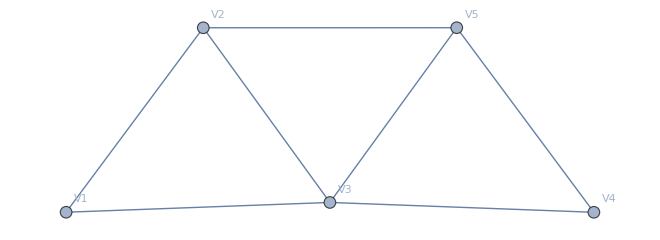
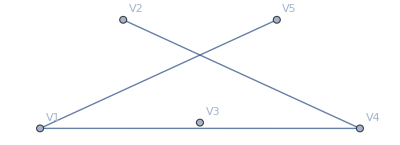

2.9999999950344276

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order:

> X11<X12<X13<X14<X15<X21<X22<X23<X24<X25<X31<X32<X33<X34<X35

* Reduce and normalize initial set

> Initial set reduced to '132' out of '294' polynomials

* Computing initial set of obstructions

> MAJOR Iteration 1, 98 polys in the basis, 235 obstructions

* Found Groebner basis with 98 polynomials

* * * * * * * * * * * * * * * *

{1,X11,X12,X13,X14,X21,X22,X23,X24,X31,X32,X11**X22,X12**X21,X12**X23,X12**X31,X13**X22,X13**X24,X13**X32}

Violation!{1,4}(0
1
0
0
0
1
0
0
0
1
0
0
0
0
0
0
0
0)(1
1
0
1
1
1
0
1
1
1
0
1
1
1
1
1
1
1)

(3 | 0 | 3 | 3 | 0
0 | 3 | 3 | 0 | 3
3 | 3 | 18 | 15 | 15
3 | 0 | 15 | 15 | 12
0 | 3 | 15 | 12 | 15)

3

(6 | 0 | 6 | 6 | 0
0 | 0 | 0 | 0 | 0
6 | 0 | 6 | 6 | 0
6 | 0 | 6 | 6 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Table[{NCExpandReplaceRepeated[Flatten[X][[i]], rels]}, {i, 1, Length[Flatten[X]]}] // MatrixForm
```

(X11
0
0
X14
1-X11-X14
X21
0
0
X24
1-X21-X24
1-X11-X21
0
0
1-X14-X24
-1+X11+X14+X21+X24)

```mathematica
basis
```

{1,X11,X12,X13,X14,X21,X22,X23}

```mathematica
Lovasz[GraphComplement[rg]]
```

2.999999997521012

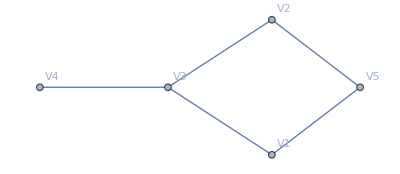
```mathematica
GraphComplement[-Graphics-]
```

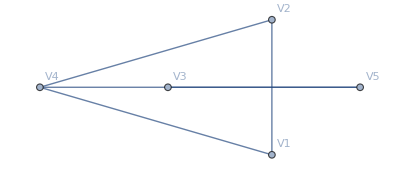

```mathematica
X
```

{{X11,X12,X13,X14,X15},{X21,X22,X23,X24,X25},{X31,X32,X33,X34,X35}}

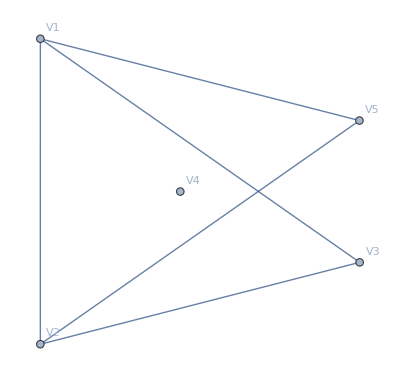

```mathematica
GraphComplement[rg]
```

```mathematica
V = {{{0, 1, 1, 0}}, {{1, 1, 1, 1}}, {{1, 0, 0, 1}}};
BV = ConstantArray[0, {3, 3}];
Do[
Do[
BV[[i, j]] = (V[[i]].Transpose[V[[j]]])[[1, 1]], {j, 1, 3}
], {i, 1, 3}
]
BV // MatrixForm
```

(2 | 2 | 0
2 | 4 | 2
0 | 2 | 2)

```mathematica
iso = res[[3]];
Do[
Print[
MatrixForm[iso[[i]]], " ", Flatten[X][[i]]
], {i, 1, Length[iso]}
]
```

```mathematica
RepRels = rels /. Rule->Subtract;
```

{-1+X11+X12+X13+X14+X15,-1+X13+X14+X23+X24,-X13-X14+X21+X22+X25,-X11+X11^2,X11**X12,X11**X13,X11**X14,X11**X21,X11**X22,-X11+X11**X23,X12**X11,-X12+X12^2,X12**X13,X12**X14,X12**X21,X12**X22,1-X12-X13-X14-X23+X12**X23,X13**X11,X13**X12,-X13+X13^2,X13**X14,-X21+X13**X21,X14-X22+X13**X22,X13**X23,X14**X11,X14**X12,X14**X13,-X14+X14^2,X14**X21,-X14+X14**X22,X14**X23,X21**X11,X21**X12,-X21+X21**X13,X21**X14,-X21+X21^2,X21**X22,X21**X23,X22**X11,X22**X12,X14-X22+X22**X13,-X14+X22**X14,X22**X21,-X22+X22^2,X22**X23,-X11+X23**X11,1-X12-X13-X14-X23+X23**X12,X23**X13,X23**X14,X23**X21,X23**X22,-X23+X23^2}

```mathematica
X
```

{{X11,X12,X13,X14,X15},{X21,X22,X23,X24,X25},{X31,X32,X33,X34,X35}}

X11 X11

X21 X21

X31 X31

X12 X12

X22 X22

X32 X32

X13 X13

X23 X23

X33 1-X13-X23

X14 X14

X24 X24

X34 1-X12-X14-X22-X24-X32

X15 1-X11-X12-X13-X14

X25 1-X21-X22-X23-X24

X35 -1+X12+X13+X14+X22+X23+X24-X31

V1: X11+X21+X31

V2: X12+X22+X32

V3: 1

V4: 1-X12-X22-X32

V5: 1-X11-X21-X31

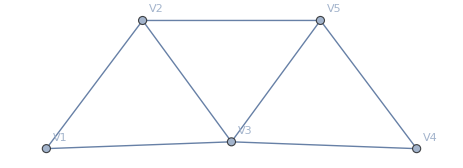

```mathematica
Vnum = Length[X[[1]]];
overallVs  = Table[0, {v, 1, Vnum}];
Do[
expr = 0;
Do[
expr =expr + NCExpandReplaceRepeated[X[[i, v]], rels];
Print[" ", "X"<>ToString[i]<>ToString[v], " ", NCExpandReplaceRepeated[X[[i, v]], rels]];
, {i, 1, Length[X]}
];
overallVs[[v]] = expr, {v, 1, Vnum}
]
Do[
Print["V"<>ToString[v]<>": ", overallVs[[v]]], {v, 1, Vnum}
]
Print[rg]
```

```mathematica
X13
```

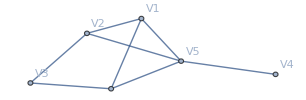
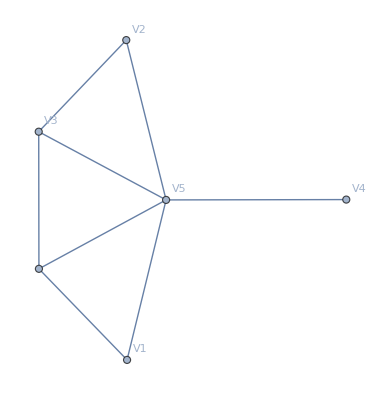
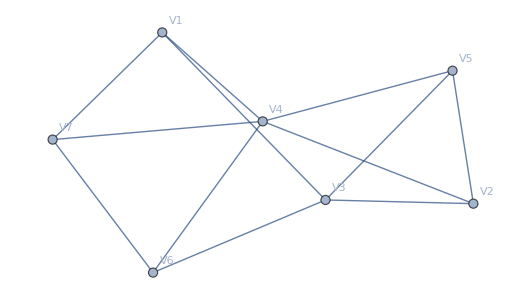
```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

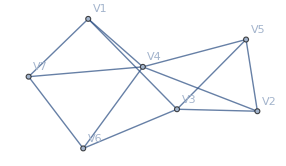
```mathematica
rg = -Graphics-;
adjrg = AdjacencyMatrix[rg];
rgv = Dimensions[adjrg][[1]];
allneighs = {};
Do[
Do[
If[
adjrg[[u, v]] == 1,
neighbours = {};
Do[
If[
adjrg[[u, w]] == 1 && adjrg[[v, w]] == 1,
AppendTo[
neighbours, w
]
], {w, 1, rgv}
];
AppendTo[
allneighs, {{u, v}, neighbours}
]
], {v, 1, rgv}
], {u, 1, rgv}
]
allneighs // ColumnForm
EdgeList[rg]
```

{{1,3},{}}
{{1,4},{7}}
{{1,7},{4}}
{{2,3},{5}}
{{2,4},{5}}
{{2,5},{3,4}}
{{3,1},{}}
{{3,2},{5}}
{{3,5},{2}}
{{3,6},{}}
{{4,1},{7}}
{{4,2},{5}}
{{4,5},{2}}
{{4,6},{7}}
{{4,7},{1,6}}
{{5,2},{3,4}}
{{5,3},{2}}
{{5,4},{2}}
{{6,3},{}}
{{6,4},{7}}
{{6,7},{4}}
{{7,1},{4}}
{{7,4},{1,6}}
{{7,6},{4}}

{1<->3,1<->4,1<->7,2<->3,2<->4,2<->5,3<->5,3<->6,4<->5,4<->6,4<->7,6<->7}

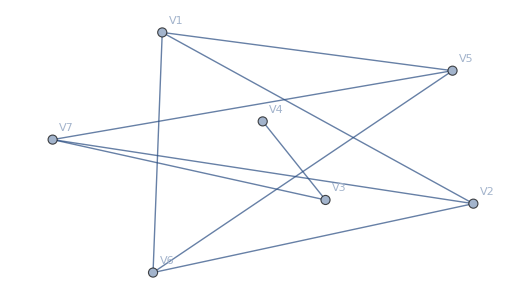

```mathematica
GraphComplement[-Graphics-]
```

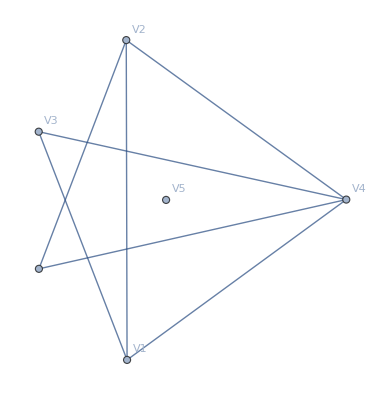

```mathematica
GraphComplement[-Graphics-]
```

```mathematica
rels /. Rule->Subtract
```

{}

```mathematica
basis
```

{1}